```mathematica
(* ====== Liberia ====== *)
ClearAll[n,d,A,M,S,U,p,q,a,x,Udata,Mdata,Adata,Ddata,Sdata];
n=3441790;
Udata = {2582,2591,2600,2613,2626,2638,2651,2664,2664,2663,2666,2668,2671,2674,2676,2679,2682,2684,2687,2704,2720,2827,2935,2962,2972,2982,2993,3007,3013,3029,3035,3045,3055,3067,3067,3061,3056,3050,3050,3050,3042,3034,3020,3005,2991,2991,3020,3020,3020,3045,3071,3096,3096,3132,3132,3132,3154,3176,3198,3223,3223,3232,3309,3313,3318,3322,3322,3365,3394,3394,3414,3434,3454,3489,3489,3534,3534,3534,3534,3534,3620,3620,3641,3641,3649,3658,3666,3717,3732,3732}
Mdata = {1687,1702,1716,1725,1734,1744,1753,1762,1756,1750,1750,1751,1751,1752,1752,1753,1753,1754,1754,1763,1771,1778,1785,1792,1792,1792,1792,1809,1811,1812,1814,1814,1814,1829,1829,1820,1810,1801,1801,1801,1783,1764,1761,1757,1754,1754,1757,1757,1757,1762,1768,1773,1773,1776,1776,1776,1786,1795,1805,1816,1816,1816,1831,1832,1832,1833,1833,1839,1841,1841,1844,1847,1850,1854,1854,1854,1854,1854,1854,1854,1864,1864,1864,1864,1864,1864,1864,1869,1870,1870}
Adata = {2553,2558,2562,2578,2594,2611,2627,2643,2656,2669,2675,2682,2688,2695,2701,2708,2714,2721,2727,2740,2753,2769,2785,2801,2801,2801,2805,2824,2826,2828,2830,2830,2830,2869,2869,2895,2920,2946,2946,2946,2984,3021,3042,3064,3085,3085,3085,3085,3085,3093,3100,3108,3108,3110,3110,3110,3112,3114,3116,3118,3118,3118,3123,3123,3123,3123,3123,3127,3127,3127,3128,3130,3131,3135,3135,3136,3136,3136,3136,3136,3138,3138,3138,3138,3138,3138,3138,3143,3143,3143}
Ddata = {2812,2824,2836,2862,2887,2913,2938,2963,2964,2964,2969,2975,2981,2987,2992,2998,3004,3010,3016,3023,3029,3068,3106,3145,3145,3145,3155,3161,3166,3172,3177,3177,3177,3222,3222,3245,3267,3290,3290,3290,3318,3346,3356,3366,3376,3376,3384,3384,3384,3394,3404,3413,3413,3423,3423,3423,3439,3455,3471,3496,3496,3496,3515,3515,3515,3515,3515,3538,3556,3556,3566,3577,3587,3605,3605,3636,3636,3636,3636,3636,3686,3686,3700,3700,3703,3707,3710,3739,3740,3746}
Sdata = {3432156,3432115,3432076,3432012,3431949,3431884,3431821,3431758,3431750,3431744,3431730,3431714,3431699,3431682,3431669,3431652,3431637,3431621,3431606,3431560,3431517,3431348,3431179,3431090,3431080,3431070,3431045,3430989,3430974,3430949,3430934,3430924,3430914,3430803,3430803,3430769,3430737,3430703,3430703,3430703,3430663,3430625,3430611,3430598,3430584,3430584,3430544,3430544,3430544,3430496,3430447,3430400,3430400,3430349,3430349,3430349,3430299,3430250,3430200,3430137,3430137,3430128,3430012,3430007,3430002,3429997,3429997,3429921,3429872,3429872,3429838,3429802,3429768,3429707,3429707,3429630,3429630,3429630,3429630,3429630,3429482,3429482,3429447,3429447,3429436,3429423,3429412,3429322,3429299,3429299}
ϵ=Sum[(Udata[[i+1]]-Udata[[i]]+p*Udata[[i]]-x/n*Sdata[[i]]*(Mdata[[i]]+Adata[[i]]))^2,{i,Length@Udata-1}]
N@Minimize[ϵ,{x,p}]
```

{2582,2591,2600,2613,2626,2638,2651,2664,2664,2663,2666,2668,2671,2674,2676,2679,2682,2684,2687,2704,2720,2827,2935,2962,2972,2982,2993,3007,3013,3029,3035,3045,3055,3067,3067,3061,3056,3050,3050,3050,3042,3034,3020,3005,2991,2991,3020,3020,3020,3045,3071,3096,3096,3132,3132,3132,3154,3176,3198,3223,3223,3232,3309,3313,3318,3322,3322,3365,3394,3394,3414,3434,3454,3489,3489,3534,3534,3534,3534,3534,3620,3620,3641,3641,3649,3658,3666,3717,3732,3732}

{1687,1702,1716,1725,1734,1744,1753,1762,1756,1750,1750,1751,1751,1752,1752,1753,1753,1754,1754,1763,1771,1778,1785,1792,1792,1792,1792,1809,1811,1812,1814,1814,1814,1829,1829,1820,1810,1801,1801,1801,1783,1764,1761,1757,1754,1754,1757,1757,1757,1762,1768,1773,1773,1776,1776,1776,1786,1795,1805,1816,1816,1816,1831,1832,1832,1833,1833,1839,1841,1841,1844,1847,1850,1854,1854,1854,1854,1854,1854,1854,1864,1864,1864,1864,1864,1864,1864,1869,1870,1870}

{2553,2558,2562,2578,2594,2611,2627,2643,2656,2669,2675,2682,2688,2695,2701,2708,2714,2721,2727,2740,2753,2769,2785,2801,2801,2801,2805,2824,2826,2828,2830,2830,2830,2869,2869,2895,2920,2946,2946,2946,2984,3021,3042,3064,3085,3085,3085,3085,3085,3093,3100,3108,3108,3110,3110,3110,3112,3114,3116,3118,3118,3118,3123,3123,3123,3123,3123,3127,3127,3127,3128,3130,3131,3135,3135,3136,3136,3136,3136,3136,3138,3138,3138,3138,3138,3138,3138,3143,3143,3143}

{2812,2824,2836,2862,2887,2913,2938,2963,2964,2964,2969,2975,2981,2987,2992,2998,3004,3010,3016,3023,3029,3068,3106,3145,3145,3145,3155,3161,3166,3172,3177,3177,3177,3222,3222,3245,3267,3290,3290,3290,3318,3346,3356,3366,3376,3376,3384,3384,3384,3394,3404,3413,3413,3423,3423,3423,3439,3455,3471,3496,3496,3496,3515,3515,3515,3515,3515,3538,3556,3556,3566,3577,3587,3605,3605,3636,3636,3636,3636,3636,3686,3686,3700,3700,3703,3707,3710,3739,3740,3746}

{3432156,3432115,3432076,3432012,3431949,3431884,3431821,3431758,3431750,3431744,3431730,3431714,3431699,3431682,3431669,3431652,3431637,3431621,3431606,3431560,3431517,3431348,3431179,3431090,3431080,3431070,3431045,3430989,3430974,3430949,3430934,3430924,3430914,3430803,3430803,3430769,3430737,3430703,3430703,3430703,3430663,3430625,3430611,3430598,3430584,3430584,3430544,3430544,3430544,3430496,3430447,3430400,3430400,3430349,3430349,3430349,3430299,3430250,3430200,3430137,3430137,3430128,3430012,3430007,3430002,3429997,3429997,3429921,3429872,3429872,3429838,3429802,3429768,3429707,3429707,3429630,3429630,3429630,3429630,3429630,3429482,3429482,3429447,3429447,3429436,3429423,3429412,3429322,3429299,3429299}

(3732 p-(17191075887 x)/3441790)^2+(15+3717 p-(8593880932 x)/1720895)^2+(3620 p-(8577134482 x)/1720895)^2+(21+3620 p-(8577134482 x)/1720895)^2+(3641 p-(8577046947 x)/1720895)^2+(8+3641 p-(8577046947 x)/1720895)^2+(9+3649 p-(8577019436 x)/1720895)^2+(8+3658 p-(8576986923 x)/1720895)^2+(51+3666 p-(8576959412 x)/1720895)^2+4 (3534 p-(1711385370 x)/344179)^2+(86+3534 p-(1711385370 x)/344179)^2+(3489 p-(17110808223 x)/3441790)^2+(45+3489 p-(17110808223 x)/3441790)^2+(35+3454 p-(8541837204 x)/1720895)^2+(20+3434 p-(8535062277 x)/1720895)^2+(20+3414 p-(775143388 x)/156445)^2+(3394 p-(8519802048 x)/1720895)^2+(20+3394 p-(8519802048 x)/1720895)^2+(29+3365 p-(774226713 x)/156445)^2+(3322 p-(8499532566 x)/1720895)^2+(43+3322 p-(8499532566 x)/1720895)^2+(5+3313 p-(3399136937 x)/688358)^2+(4+3318 p-(1699565991 x)/344179)^2+(4+3309 p-(8496139724 x)/1720895)^2+(3223 p-(8462147979 x)/1720895)^2+(9+3223 p-(8462147979 x)/1720895)^2+(77+3232 p-(8462125776 x)/1720895)^2+(25+3198 p-(1688001420 x)/344179)^2+(22+3176 p-(1683909725 x)/344179)^2+(22+3154 p-(8400802251 x)/1720895)^2+2 (3132 p-(8380342607 x)/1720895)^2+(22+3132 p-(8380342607 x)/1720895)^2+(3096 p-(24990720 x)/5137)^2+(36+3096 p-(24990720 x)/5137)^2+(25+3071 p-(8349707998 x)/1720895)^2+(26+3045 p-(1665505808 x)/344179)^2+2 (3020 p-(8305347024 x)/1720895)^2+(25+3020 p-(8305347024 x)/1720895)^2+(2991 p-(8300297988 x)/1720895)^2+(29+2991 p-(8300297988 x)/1720895)^2+(-14+3005 p-(8269456479 x)/1720895)^2+(-15+3020 p-(16477224633 x)/3441790)^2+(-14+3034 p-(298464375 x)/62578)^2+(-8+3042 p-(16353970521 x)/3441790)^2+(-8+3050 p-(16285547141 x)/3441790)^2+2 (3050 p-(16285547141 x)/3441790)^2+(-6+3056 p-(147521691 x)/31289)^2+(-5+3061 p-(3235215167 x)/688358)^2+(-6+3067 p-(8058956247 x)/1720895)^2+(3067 p-(8058956247 x)/1720895)^2+(10+3035 p-(7966628748 x)/1720895)^2+(10+3045 p-(7966605528 x)/1720895)^2+(12+3055 p-(7966582308 x)/1720895)^2+(6+3029 p-(1591960336 x)/344179)^2+(16+3013 p-(7954713219 x)/1720895)^2+(6+3007 p-(15895772037 x)/3441790)^2+(14+2993 p-(3154502773 x)/688358)^2+(10+2962 p-(1575899637 x)/344179)^2+(10+2972 p-(1575895044 x)/344179)^2+(11+2982 p-(23520753 x)/5137)^2+(27+2935 p-(1568048803 x)/344179)^2+(108+2827 p-(7801169678 x)/1720895)^2+(107+2720 p-(7762091454 x)/1720895)^2+(16+2704 p-(140475588 x)/31289)^2+(17+2687 p-(114753929 x)/25685)^2+(3+2684 p-(3071300795 x)/688358)^2+(2+2682 p-(1393556589 x)/312890)^2+(3+2679 p-(7654299786 x)/1720895)^2+(3+2676 p-(15281222057 x)/3441790)^2+(2+2674 p-(7630344927 x)/1720895)^2+(3+2671 p-(15233311861 x)/3441790)^2+(3+2668 p-(691490371 x)/156445)^2+(2+2666 p-(1518540525 x)/344179)^2+(3+2663 p-(7582438368 x)/1720895)^2+(-1+2664 p-(1514088100 x)/344179)^2+(2664 p-(137426309 x)/31289)^2+(13+2651 p-(1503137598 x)/344179)^2+(13+2638 p-(22307246 x)/5137)^2+(12+2626 p-(7426737636 x)/1720895)^2+(13+2613 p-(7383973818 x)/1720895)^2+(13+2600 p-(7341210564 x)/1720895)^2+(9+2591 p-(1462080990 x)/344179)^2+(9+2582 p-(1455234144 x)/344179)^2

{42664.5,{x→0.000518139,p→-0.00338363}}

```mathematica
p=0.006021251370836927
ϵ=Sum[(Udata[[i+1]]-Udata[[i]]+p*Udata[[i]]-x/n*Sdata[[i]]*(Mdata[[i]]+Adata[[i]]))^2,{i,Length@Udata-1}]
N@Minimize[ϵ,{x}]
```

0.00602125

{42962.3,{x→0.00669021}}

```mathematica
ClearAll[ϵ,q]
q=0.009379024655119134;
ϵ=Sum[(Mdata[[i+1]]-Mdata[[i]]+q*Mdata[[i]]-p*Udata[[i]])^2,{i,Length@Udata-1}]
(*Plot[ϵ[x],{x,-0.0001,0.0001}]*)
(*For[q=0,q<50,q++,Print[ϵ]]*)
N@Minimize[{ϵ},{p}]
```

{3733.45,{p→0.00602125}}

```mathematica
ClearAll[ϵ]
a = 0.0034935360032437367;
ϵ=Sum[(Adata[[i+1]]-Adata[[i]]+a*Adata[[i]]-q*Mdata[[i]])^2,{i,Length@Ddata-1}]
N@Minimize[ϵ,{q}]
```

{7406.61,{q→0.00937902}}

```mathematica
ClearAll[ϵ]
ϵ=Sum[(Ddata[[i+1]]-Ddata[[i]]-a*Adata[[i]])^2,{i,Length@Ddata-1}]
N@Minimize[ϵ,{a}]
```

{12818.,{a→0.00349354}}

```mathematica
Flatten[{3633.9650522701822,{a->0.004093830941444588}}]
```

{3633.97,a→0.00409383}

0.00669021

0.00602125

0.00937902

0.00349354

3441790

{{S→InterpolatingFunction[{{0.,90.}},<>],U→InterpolatingFunction[{{0.,90.}},<>],M→InterpolatingFunction[{{0.,90.}},<>],A→InterpolatingFunction[{{0.,90.}},<>],d→InterpolatingFunction[{{0.,90.}},<>]}}

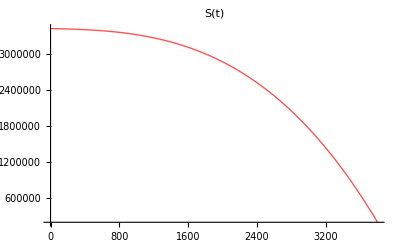

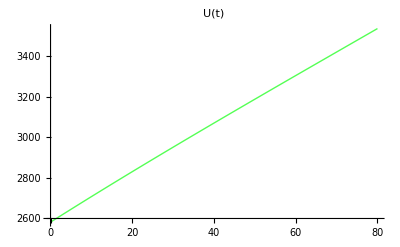

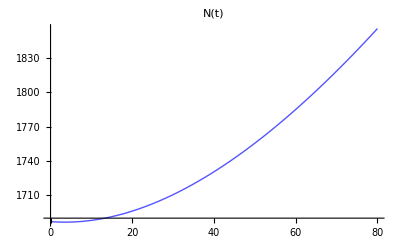

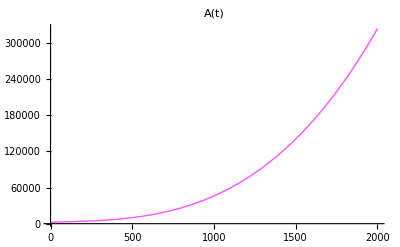

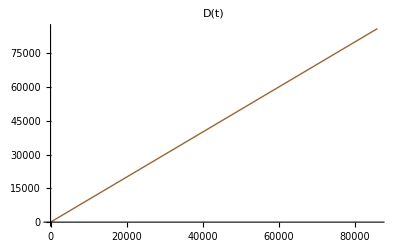

```mathematica
x=0.00669021
p=0.00602125
q=0.00937902
a=0.00349354
n=3441790
eq= NDSolve[{U'[t]==x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==2582,M[0]==1687,A[0]==2553,d[0]==2812,S[0]==3432156},{S,U,M,A,d},{t,0,90}]
SetOptions[Plot,BaseStyle->{FontSize->14}];
Plot[{(S[t]/.eq)},{t,0,3800},PlotRange->All,PlotLabel->"S(t)",PlotStyle->{Lighter[Red],Thick}]
Plot[{(U[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"U(t)",PlotStyle->{Lighter[Green],Thick}]
Plot[{(M[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"N(t)",PlotStyle->{Lighter[Blue],Thick}]
Plot[{(A[t]/.eq)},{t,0,2000},PlotRange->All,PlotLabel->"A(t)",PlotStyle->{Lighter[Magenta],Thick}]
Plot[{(D[t]/.eq)},{t,0,86000},PlotRange->All,PlotLabel->"D(t)",PlotStyle->{Brown,Thick}]
```

```mathematica
1.3*10^6
```

1.3×10^6

```mathematica
"
```